## Periodic chain

```mathematica
(* Tight-binding Hamiltonian for a tranlational invariant chain, with periodic bc *)
h[n_,V_]:=Block[{tbl,ar,mid=IntegerPart[n/2]},
(* jump amplitudes *)
tbl=Table[{i,i+1}->1.,{i,1,n-1}];
(* periodic bc *)
AppendTo[tbl,{1,n}->-1.];
(* scalar impurity at the middle of the chain *)
AppendTo[tbl,{mid,mid}->V/2];
ar=SparseArray[tbl,{n,n}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* wavefunctions and energies *)
n=500;
v=.1;
{en,eigs}=Eigensystem[h[n,v]];
ord=Ordering[en];
(* order eigenfunctions by increasing energy *)
eigs=eigs[[ord]];
en=en[[ord]];

{enRef,eigsRef}=Eigensystem[h[n,0.]];
ordRef=Ordering[enRef];
eigsRef=eigsRef[[ordRef]];
enRef=enRef[[ordRef]];
```

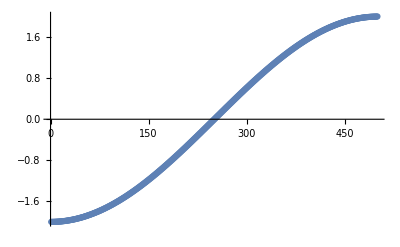

```mathematica
ListPlot[en]
```

### Local density of states (physically meaningless)

```mathematica
(* approximate Dirac delta *)
δ[x_,ϵ_]:=(ϵ/Pi)/(x^2+ϵ^2);
(*δ[x_,ϵ_]:=Max[1-Abs[x/ϵ],0]/ϵ;*)
```

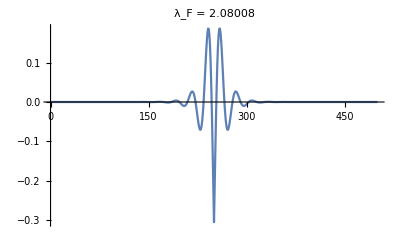

```mathematica
(* local density of states ρ(ω) for ω ∈ Spectrum *)
(*Clear[pos];
pos[i_]:=(2Pi/√(2Abs[enRef[[i]]]))^-1 Range[n];*)
ω=en[[20]];
(* index wavefunctions by energies, take their square *)
int=Transpose[eigs]^2;
intRef=Transpose[eigsRef]^2;
ϵ=0.01;
deltalist=δ[ω-#,ϵ]&/@en;
deltalistRef=δ[ω-#,ϵ]&/@enRef;
(* local density of states: Subscript[ρ, ii](ω) = Subscript[Σ, a] int(i,a)^2 Subscript[δ, ϵ](ω-Subscript[E, a]) *)
rho=int.deltalist;
(* local density in absence of impurity *)
rhoRef=intRef.deltalistRef;
(* change in density when we add the impurity *)
drho=rho-rhoRef;
λf=(2Pi)/ArcCos[ω/2];
ListPlot[drho,PlotRange->All,Joined->True,PlotLabel->"λ_F = "<>ToString[λf]]
(*Plot[(λf/2) drho[[IntegerPart[n/2]]]Sin[2 (x-n/2)/λf]/(x-n/2),{x,0,n},Epilog->Point@MapThread[{#1,#2}&,{Range[n],drho}],PlotRange->All]*)
```

### Integrated local density of states

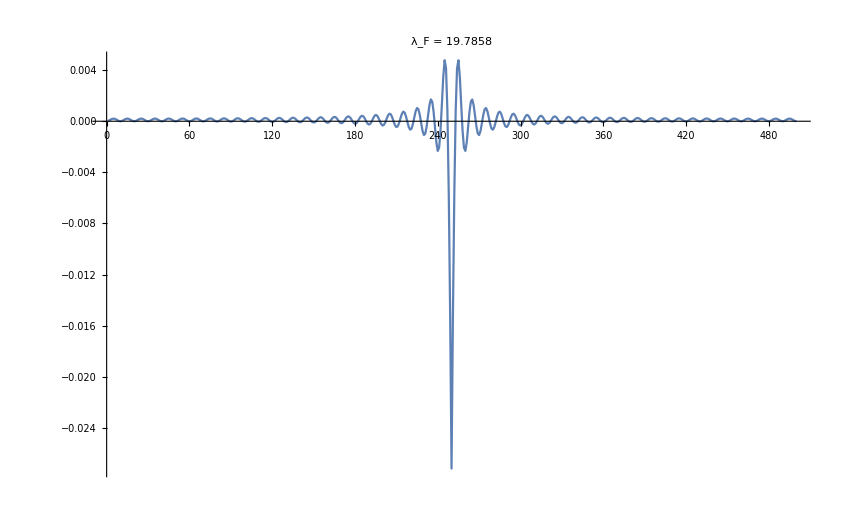

```mathematica
(* chemical potential *)
mu=1.9;
(* find the index of the lowest energy level larger than the chemical potential *)
FirstPosition[en,e_ /; e>mu]//First;
(* index of the highest energy level smaller than the chemical potential *)
If[%=="NotFound",am=n,am=%-1];
(* index wavefunctions by energies, keep components up to the Fermi level, take their square *)
int=(eigs[[;;am]])^2;

FirstPosition[enRef,e_ /; e>mu]//First;
If[%=="NotFound",am=n,am=%-1];
intRef=(eigsRef[[;;am]])^2;
(* difference in integrated local density of states *)
dPhi=(Plus@@int)-(Plus@@intRef);
(* wavelength at the Fermi level *)
λf=(2Pi)/ArcCos[mu/2];
ListPlot[dPhi,PlotRange->All,Joined->True,PlotLabel->"λ_F = "<>ToString[λf]]
```

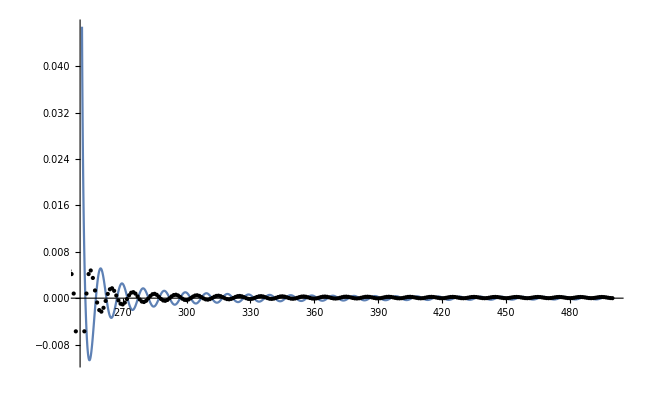

```mathematica
th[x_]:=(v λf)/(2Pi)^2 Cos[(4 Pi (x-n/2))/λf]/(x-n/2);
Plot[th[x],{x,n/2+.9,n},Epilog->Point@MapThread[{#1,#2}&,{Range[n],dPhi}],PlotRange->All]
```

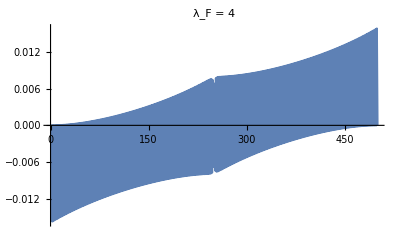

```mathematica
(* relative distance to the impurity *)
relx=Table[i-IntegerPart[n/2],{i,1,n}];
(* integrated densiy of states times the relative distance *)
dPhix=relx*dPhi;
ListPlot[dPhix,PlotRange->All,Joined->True,PlotLabel->"λ_F = "<>ToString[λf]]
```

## Fibonacci in the direct basis

```mathematica
τ=N [(1+Sqrt[5])/2];
rot=0;
fib[n_]:=IntegerPart[τ^-1( n+1+rot)]-IntegerPart[τ^-1 (n+rot)];
jump[n_,tw_]:=If[fib[n-1]<1,1.,tw];
```

```mathematica
Clear[hf];
(* s: site of the perturbation *)
hf[n_,tw_,s_,V_]:=Block[{F2=Fibonacci[n+2],tbl,ar},
(* jump amplitudes *)
tbl=Table[{i,i+1}->jump[i,tw],{i,1,F2-1}];
(* periodic boundary conditions *)
AppendTo[tbl,{1,F2}->tw];
(* scalar impurity at the site s *)
AppendTo[tbl,{s,s}->V/2];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* take a renormalization path (seq), a site label (i) and an approximant size (n) and return the new renormalization path, the new site label and the new size after one renormalization group operation *)
iterSeq[{seq_,i_,n_}]:=Block[{inew=i,seqn=seq,nnew=n},
If[i>Fibonacci[n-1],seqn="m"<>seq;inew=i-Fibonacci[n-1];nnew=n-2;,
If[i>Fibonacci[n-2],seqn="a"<>seq;inew=i-Fibonacci[n-2];nnew=n-3,
seqn="m"<>seq;nnew=n-2;]];
{seqn,inew,nnew}
]
(* false when n<3 *)
test=#[[3]]≥3&;
(* variant where we forget about the site number *)
path[i_,n_]:=NestWhile[iterSeq,{"",i,n},test][[1]]
(* Display all the paths for a system size *)
paths[n_]:=path[#,n]&/@Range[Fibonacci[n]]
```

```mathematica
(* impurity at every site having the same renormalization path as s *)
ht[n_,tw_,s_,V_]:=Block[{F2=Fibonacci[n+2],tbl,ar,pos,pths,imp},
(* jump amplitudes *)
tbl=Table[{i,i+1}->jump[i,tw],{i,1,F2-1}];
(* periodic boundary conditions *)
AppendTo[tbl,{1,F2}->tw];
(* list of renormalization paths *)
pths=paths[n+2];
(* positions of the impurities *)
pos=Position[pths,pths[[s]]]//Flatten;
(* place the impurities in the Hamiltonian *)
imp=Table[{i,i}->V,{i,pos}];
ar=SparseArray[tbl,{F2,F2}];
imp=SparseArray[imp,{F2,F2}];
Normal[ar+Transpose[ar]+imp]
]
```

### Oscillations in direct space in the weak quasiperiodicity limit

```mathematica
(* wavefunctions and energies *)
n=10;
(* weak qp: Subscript[t, w] -> 1 *)
tw=.5;
v=1.;
s=50;
{en,eigs}=Eigensystem[hf[n,tw,s,v]];
ord=Ordering[en];
(* order eigenfunctions by increasing energy *)
eigs=eigs[[ord]];
en=en[[ord]];

v=0.;
{enRef,eigsRef}=Eigensystem[hf[n,tw,s,v]];
ordRef=Ordering[enRef];
eigsRef=eigsRef[[ordRef]];
enRef=enRef[[ordRef]];
```

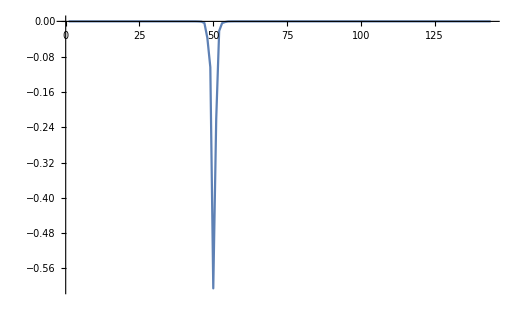

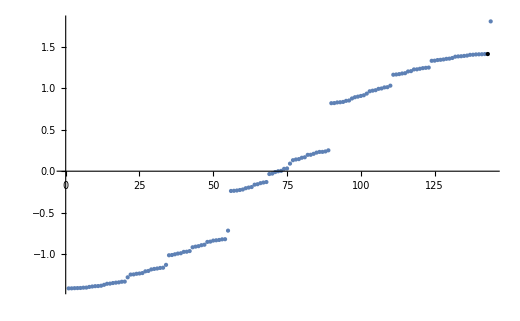

```mathematica
(* chemical potential *)
mu=1.6;
(* find the index of the lowest energy level larger than the chemical potential *)
FirstPosition[en,e_ /; e>mu]//First;
(* index of the highest energy level smaller than the chemical potential *)
If[%=="NotFound",am=-1,am=%-1];
(* index wavefunctions by energies, keep components up to the Fermi level, take their square *)
int=(eigs[[;;am]])^2;

FirstPosition[enRef,e_ /; e>mu]//First;
If[%=="NotFound",amRef=-1,amRef=%-1];
intRef=(eigsRef[[;;amRef]])^2;
(* difference in integrated local density of states *)
dPhi=(Plus@@int)-(Plus@@intRef);
(* wavelength at the Fermi level *)
λf=(2Pi)/ArcCos[mu/2-1];
ListPlot[dPhi,PlotRange->All,Joined->True]

ListPlot[en,Epilog->{PointSize[Medium],Point[{am,en[[am]]}]},PlotStyle->PointSize[Medium]]
```

### Average on energies having the same renormalization path

```mathematica
(* take a renormalization path (seq), a site label (i) and an approximant size (n) and return the new renormalization path, the new site label and the new size after one renormalization group operation *)
iterSeq[{seq_,i_,n_}]:=Block[{inew=i,seqn=seq,nnew=n},
If[i>Fibonacci[n-1],seqn="m"<>seq;inew=i-Fibonacci[n-1];nnew=n-2;,
If[i>Fibonacci[n-2],seqn="a"<>seq;inew=i-Fibonacci[n-2];nnew=n-3,
seqn="m"<>seq;nnew=n-2;]];
{seqn,inew,nnew}
]
```

```mathematica
(* false when n<3 *)
test=#[[3]]≥3&;
(* take a site (i), a size (n) and return the renormalization path for this site *)
path[i_,n_]:=NestWhile[iterSeq,{"",i,n},test][[1]]->i
(* variant where we forget about the site number *)
path2[i_,n_]:=NestWhile[iterSeq,{"",i,n},test][[1]]
(* compute the relative time spent on molecular sites (x) *)
xPath[i_,n_]:={i,StringCount[NestWhile[iterSeq,{"",i,n},test][[1]],"m"]/n}
(* variant where we forget about the site number *)
xPath2[i_,n_]:=StringCount[NestWhile[iterSeq,{"",i,n},test][[1]],"m"]/n
```

```mathematica
(* generate the whole (x) tree! *)
tree[n_]:=xPath[#,n]&/@ Range[Fibonacci[n]]
(* variant where we forget about the site number, and compute nx rather than x *)
tree2[n_]:=n xPath2[#,n]&/@ Range[Fibonacci[n]]
```

```mathematica
(* Display all the paths for a system size *)
paths[n_]:=path2[#,n]&/@Range[Fibonacci[n]]
```

```mathematica
(* chose a chemical potential *)
mu=1.2;
(* find the index of the lowest energy level larger than the chemical potential *)
FirstPosition[en,e_ /; e>mu]//First;
(* index of the highest energy level smaller than the chemical potential *)
If[%=="NotFound",am=n,am=%-1];
(* indexes of the energies having the same renormalization path *)
p=paths[n+2];
simE=Position[p,p[[am]]]//Flatten;
(* index wavefunctions by energies, keep components up to the Fermi level, take their square *)
intL=(eigs[[;;#]])^2&/@simE;
intRefL=(eigsRef[[;;#]])^2&/@simE;
(* difference in integrated local density of states *)
dPhiL=MapThread[((Plus@@#1)-(Plus@@#2))&,{intL,intRefL}];
```

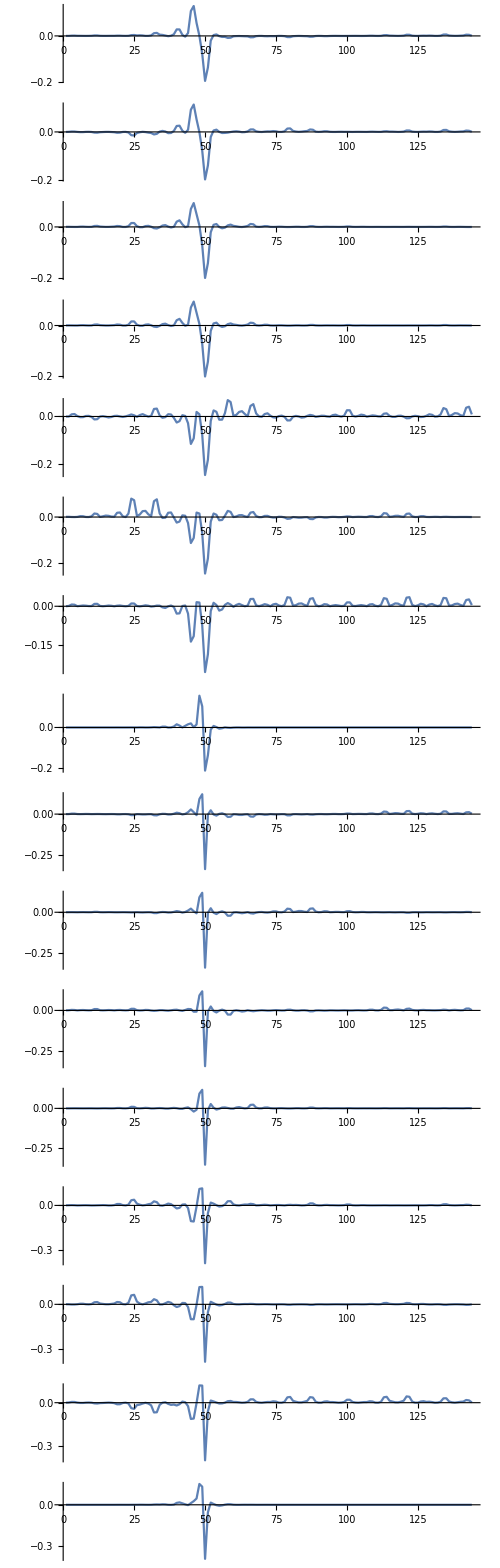

```mathematica
GraphicsColumn[ListPlot[#,Joined->True,PlotRange->All]&/@dPhiL,ImageSize->500]
```

```mathematica
p[[am]]
```

ammmm

```mathematica
simE
```

{2,7,15,20,36,41,49,54,91,96,104,109,125,130,138,143}

### Fixed impurity site, varying chemical potential

```mathematica
(* find the position of the last filled energy level *)
lastLvl[sp_,mu_]:=Block[{last,L=Length[sp]},
(* find the index of the lowest energy level larger than the chemical potential *)
last=FirstPosition[sp,e_ /; e>mu]//First;
(* index of the highest energy level smaller or equal to the chemical potential *)
If[last=="NotFound",last=L,last=last-1];
last
]
```

```mathematica
(* return energies and eigenfunctions *)
valvec[n_,ρ_,v_,s_]:=Block[{ord,val,vec},
{val,vec}=Eigensystem[hf[n,ρ,s,v]];
ord=Ordering[val];
(* order eigenfunctions by increasing energy *)
{val[[ord]],vec[[ord]]}
]
```

```mathematica
(* return energies and eigenfunctions *)
valvec2[n_,ρ_,v_,s_]:=Block[{ord,val,vec},
{val,vec}=Eigensystem[ht[n,ρ,s,v]];
ord=Ordering[val];
(* order eigenfunctions by increasing energy *)
{val[[ord]],vec[[ord]]}
]
```

```mathematica
(* variation in integrated density of states δN(μ;V,s) = N(μ;V,s)-N(μ;0) *)
idos[n_,ρ_,mu_,v_,s_]:=Block[{en,eigs,am,int},
{en,eigs}=valvec[n,ρ,v,s];
am=lastLvl[en,mu];
(* intensities up to the last filled level *)
int=(eigs[[;;am]])^2;
(* δN *)
Total[int]
]
```

```mathematica
(* variation in integrated density of states δN(μ;V,s) = N(μ;V,s)-N(μ;0) *)
idos2[n_,ρ_,mu_,v_,s_]:=Block[{en,eigs,am,int},
{en,eigs}=valvec2[n,ρ,v,s];
am=lastLvl[en,mu];
(* intensities up to the last filled level *)
int=(eigs[[;;am]])^2;
(* δN *)
Total[int]
]
```

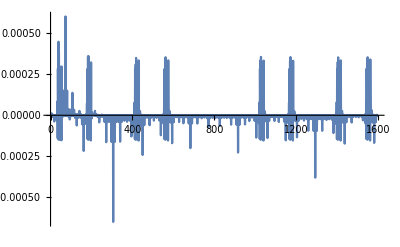

```mathematica
mu=0.;
s=49;
n=15;
ρ=.5;
δN=idos2[n,ρ,mu,-.001,s]-idos2[n,ρ,mu,0.,s];
ListPlot[δN,PlotRange->All,Joined->True]
```

In conumbering

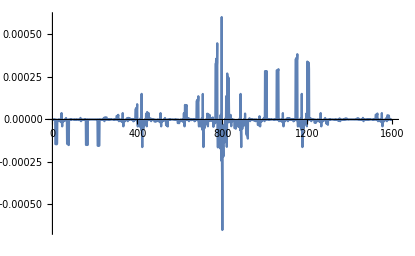

```mathematica
p=Fibonacci[n];
q=Fibonacci[n+1];
conum[n_]:=Mod[q n,p+q];
(* sites in conumbering *)
co=conum/@Range[0,p+q-1]+1;
(* permutation from co to direct basis *)
perm=Table[DiscreteDelta[i-co[[j]]],{i,p+q},{j,p+q}];
(* global translation to center the impurity site *)
(*half=IntegerPart[Fibonacci[n+2]/2];
perm=RotateRight[perm,half-co[[s]]];*)
(* δN in conumered basis *)
coδN=perm.δN;
ListPlot[coδN,PlotRange->All,Joined->True]
```

```mathematica
n=10;
ρ=0.1;
v=1.;
s=50;
{val,vec}=valvec[n,ρ,v,s];
mulist=val;
```

```mathematica
nmu=ParallelMap[idos[n,ρ,#,v,s]&,mulist];
n0mu=ParallelMap[idos[n,ρ,#,0.,s]&,mulist];
```

```mathematica
δNmu=nmu-n0mu;
```

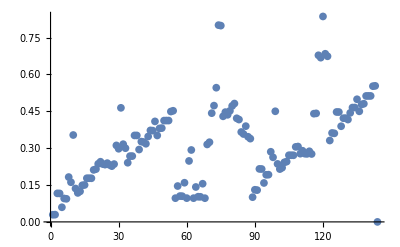

```mathematica
ListPlot[Total/@((δNmu)^2),PlotRange->All]
```

```mathematica
tot=Total/@((δNmu)^2);
Position[tot,Max[tot]]//First//First
```

120

```mathematica
p=paths[n+2];
```

```mathematica
p[[75]]
```

amaa

```mathematica
p[[s]]
```

mmmmm

### Fixed chemical potential, varying impurity site

```mathematica
n=10;
ρ=0.1;
v=1.;
mu=1.5;
slist=Range[Fibonacci[n+2]];
```

```mathematica
δNs=ParallelMap[δN[n,ρ,mu,v,#]&,slist];
```

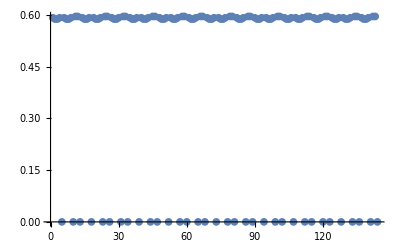

```mathematica
tot=Total/@((δNs)^2);
ListPlot[tot,PlotRange->All]
```

```mathematica
p1=Position[tot,t_ /; t<0.3]
```

{{5},{10},{13},{18},{23},{26},{31},{34},{39},{44},{47},{52},{57},{60},{65},{68},{73},{78},{81},{86},{89},{94},{99},{102},{107},{112},{115},{120},{123},{128},{133},{136},{141},{144}}

```mathematica
ll=lastLvl[valvec[n,ρ,v,#][[1]],mu]&/@slist
```

{143,143,143,143,144,143,143,143,143,144,143,143,144,143,143,143,143,144,143,143,143,143,144,143,143,144,143,143,143,143,144,143,143,144,143,143,143,143,144,143,143,143,143,144,143,143,144,143,143,143,143,144,143,143,143,143,144,143,143,144,143,143,143,143,144,143,143,144,143,143,143,143,144,143,143,143,143,144,143,143,144,143,143,143,143,144,143,143,144,143,143,143,143,144,143,143,143,143,144,143,143,144,143,143,143,143,144,143,143,143,143,144,143,143,144,143,143,143,143,144,143,143,144,143,143,143,143,144,143,143,143,143,144,143,143,144,143,143,143,143,144,143,143,144}

```mathematica
p2=Position[ll,144]
```

{{5},{10},{13},{18},{23},{26},{31},{34},{39},{44},{47},{52},{57},{60},{65},{68},{73},{78},{81},{86},{89},{94},{99},{102},{107},{112},{115},{120},{123},{128},{133},{136},{141},{144}}

```mathematica
p1==p2
```

True

```mathematica
p[[#]]&/@Flatten[p1]
```

{mammm,mmamm,mmamm,mammm,mmmam,mmmam,mmmam,mmmam,mammm,mmamm,mmamm,mammm,mmmma,mmmma,mmmma,mmmma,maaa,mmmma,mmmma,mmmma,mmmma,mammm,mmamm,mmamm,mammm,mmmam,mmmam,mmmam,mmmam,mammm,mmamm,mmamm,mammm,mmmmm}

```mathematica
totals[str_]:={StringCount[str,"m"],StringCount[str,"a"]}
```

```mathematica
tots=totals/@p;
```

```mathematica
Position[tots,{4,1}]
```

{{2},{4},{5},{7},{9},{10},{12},{13},{15},{17},{18},{20},{22},{23},{25},{26},{30},{31},{33},{34},{36},{38},{39},{41},{43},{44},{46},{47},{49},{51},{52},{54},{56},{57},{59},{60},{64},{65},{67},{68},{77},{78},{80},{81},{85},{86},{88},{89},{91},{93},{94},{96},{98},{99},{101},{102},{104},{106},{107},{109},{111},{112},{114},{115},{119},{120},{122},{123},{125},{127},{128},{130},{132},{133},{135},{136},{138},{140},{141},{143}}

```mathematica
Integrate[Exp[2I √ω]/ω,{ω,-Infinity,μ}]
```

ConditionalExpression[2 ExpIntegralEi[2 ⅈ √μ],(Im[μ]==0&&Re[μ]<0)||μ∉Reals]